## MATH 355 Calculus III Lab #1 - Polar Limaçons

### In this lab we will extend the polar plot of the cardioid given in class. This class of polar graphs is called the polar limaçon. The polar limaçon is defined by r( θ ) = a ± bSin( cθ ) or r( θ ) = a ± bCos( cθ ) Please note that the limaçon we studied in class is a special case of the polar limaçon where c = 1.

### Let' s first review the graph of the limaçon by defining r( θ ) and plotting:

```mathematica
r[θ_]:=1+Cos[θ]
PolarPlot[r[θ],{θ,0,2π}]
```

### Recall that we may add color to a graph and combine several on one set of axes:

```mathematica
r1[θ_]:=1 + 2Cos[θ]
r2[θ_]:=1 -2 Cos[θ]
r3[θ_]:=1 + 2Sin[θ]
r4[θ_]:=1 - 2Sin[θ]
p1=PolarPlot[r1[θ],{θ,0,2π},PlotStyle->RGBColor[1,0,0],PlotRange->{{-3,3},{-3,3}}]
p2=PolarPlot[r2[θ],{θ,0,2π},PlotStyle->RGBColor[0,1,0]]
p3=PolarPlot[r3[θ],{θ,0,2π},PlotStyle->RGBColor[0,0,1]]
p4=PolarPlot[r4[θ],{θ,0,2π},PlotStyle->RGBColor[1,1,0]]
Show[p1,p2,p3,p4]
```

### Also recall that PlotRange forces Mathematica to show the plot over the range given in PlotRange.

### Now let' s introduce the Manipulate function to change the a parameter in our original definition:

```mathematica
Manipulate[PolarPlot[a + Cos[θ],{θ, 0, 2π}],{a, 0, 2}]
```

```mathematica
Manipulate[PolarPlot[a + Cos[b*θ],{θ, 0, 2π}],{a, 0, 2},{b,-2,2}]
```

```mathematica
Manipulate[PolarPlot[1 + Sin[a*θ]*Cos[b*θ],{θ, 0, 2π}],{a, 0, 2},{b,-2,2}]
```

### Exercises 1. Examine r( θ ) = a + b cos( c*θ ) for various a, b, and c. What conclusions can be drawn? b seems to manipulate the radius of the loops, setting it to 2000 will draw the loops out to that point. Variable a seems to be a ratio of radius between loops. Variable c controls the number of loops. 2. Make up your own polar function. Examine the outcomes by varying 1 parameter. What are the results? I changed the variable defined as c in the problem above it appears to change the number of pedals.

Set::write: Tag Times in r\\ theta is Protected. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/write",
ButtonNote->"Set::write"]

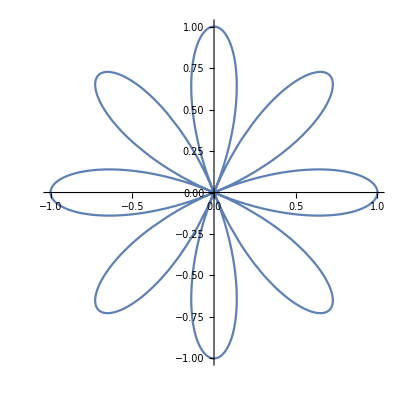

```mathematica
PolarPlot[0+Cos[4*x], {x, 0, 2Pi}]
```

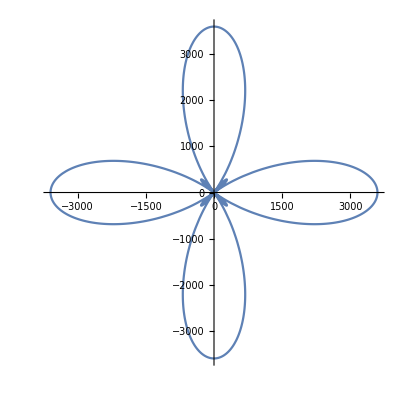

Set::write: Tag Times in r\\ x is Protected. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/write",
ButtonNote->"Set::write"]

```mathematica
PolarPlot[1600+2000Cos[4*x], {x, 0, 2Pi}]
```